THE FOLLOWING ASSUMES THAT IMPORTED DATA IS IN A TSV FORMAT OF THE FOLLOWING STYLE: X VX Y VY WITH INTEGER FREQUENCIES SERVING AS THE SEPARATION BETWEEN TEST RUNS.  CHANGES TO THIS CODE MUST TAKE THIS INTO CONSIDERATION

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
lowField12cm=Import["LowField1.2.tsv"];
lowField6cm=Import["LowField.6.tsv"];
highField12cm=Import["HighField1.2.tsv"];
highField6cm=Import["HighField.6.tsv"];
```

```mathematica
data=lowField12cm;
```

This first function finds how many frequencies were tested in the data set.

This function(plotVData) makes plots of Vy v. Vx for each frequency and places them in a list. Converts to m/s 
The count function counts how many particles survived for each frequency.
The plotPhaseSpaceXData makes phase space plots of Vx v x.
The maxboltz1D function is used to fit maxwellian distributions to the velocity data

```mathematica
getIndices[data_]:=Module[{i=1,indices={}},
While[i≤Length[data],
If[Mod[data⟦i,1⟧,1]==0,
AppendTo[indices,i];
];
i++;
];
Return[indices];
]
```

```mathematica
plotVData[data_]:=Module[{vList={},vPlots={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[vList,{data⟦i,2⟧,data⟦i,4⟧}*1000];
];
If[MemberQ[indexList,i],
AppendTo[vPlots,ListPlot[vList]];
vList={};
];
];

Return[Drop[vPlots,1]]
]
```

```mathematica
count[data_,initNumber_:1]:=Module[{counts=0,countList={},i,indexList,freq},
indexList=getIndices[data];
freq=data⟦1,1⟧;

For[i=1,i≤ Length[data],i++,

If[MemberQ[indexList,i] && i≠1,
AppendTo[countList,{freq/1000,counts/initNumber}];
freq=data⟦i,1⟧;
counts=0;
];

If[MemberQ[indexList,i]==False,
counts++;
];

If[i==Length[data],
AppendTo[countList,{data⟦Last[indexList],1⟧/1000,counts/initNumber}];
];

];

Return[countList]
]
```

```mathematica
plotPhaseSpaceXData[data_]:=Module[{psList={},psPlots={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[psList,1000*{data⟦i,1⟧,data⟦i,2⟧}];
];
If[MemberQ[indexList,i],
AppendTo[psPlots,ListPlot[psList]];
psList={};
];
];

Return[Drop[psPlots,1]]
]
```

```mathematica
maxboltz1D[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},
prob=√(m/(2 π k T)) ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

The getVelocities function grabs all of the velocity data and places it into a list.
The getPositions function does the same thing but for the positions.
The getPlotArea function uses a crude method of area approximation to find how much of a space is covered by the data.
The graphPlotAreas function takes the plot areas of the velocity graphs for each frequency measured and graphs the result.

```mathematica
getVelocities[data_]:=Module[{vList={},finalList={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[vList,{data⟦i,2⟧,data⟦i,4⟧}*1000];
];
If[MemberQ[indexList,i],
AppendTo[finalList,vList];
vList={};
];
If[i==Length[data],AppendTo[finalList,vList];];
];

Return[Drop[finalList,1]]
]
```

```mathematica
getPositions[data_]:=Module[{pList={},finalList={},i,indexList},
indexList=getIndices[data];

For[i=1,i≤ Length[data],i++,
If[MemberQ[indexList,i]==False,
AppendTo[pList,{data⟦i,1⟧,data⟦i,3⟧}];
];
If[MemberQ[indexList,i],
AppendTo[finalList,pList];
pList={};
];
If[i==Length[data],AppendTo[finalList,pList];];
];

Return[Drop[finalList,1]]
]
```

```mathematica
getPlotArea[Data_]:=Module[{x1,x2,y,area=0,i,sortedData},
sortedData=Sort[Data];
For[i=1,i<Length[Data],i++,
x1=sortedData⟦i,1⟧;
x2=sortedData⟦i+1,1⟧;
y=sortedData⟦i,2⟧;
area=area+Abs[y(x2-x1)];
];
Return[area]
]
```

```mathematica
graphPlotAreas[data_]:=Module[{areaList={},i,velocities={},frequencyList},
frequencyList=Transpose[data⟦getIndices[data]⟧]⟦1⟧/1000;
velocities=getVelocities[data];
For[i=1,i≤Length[velocities],i++,
AppendTo[areaList,{frequencyList⟦i⟧,getPlotArea[velocities⟦i⟧]}];
];
Return[ListPlot[areaList,Frame->True,FrameLabel->{"Frequency (kHz)","velocity space area (m^2/s^2)"},PlotLabel->"Velocity Space area v Frequency",ImageSize->Large,Joined->True]]
]
```

```mathematica
velData=getVelocities[data];
```

```mathematica
highField12Graph=ListPlot[count[highField12cm,20000],ImageSize->Large,Frame->True,FrameLabel->{"Frequency (Hz)","Count"},Joined->True,PlotRange->All,PlotStyle->RGBColor["Red"]];
highField6Graph = ListPlot[count[highField6cm,20000],ImageSize->Large,Frame->True,FrameLabel->{"Frequency (Hz)","Count"},PlotLabel->"Particle count v Frequency for -.6 cm^-1",Joined->True,PlotRange->All,PlotStyle->RGBColor["Black"]];
lowField6Graph=ListPlot[count[lowField6cm,20000],ImageSize->Large,Frame->True,FrameLabel->{"Frequency (Hz)","Count"},PlotLabel->"Particle count v Frequency for +.6 cm^-1",Joined->True,PlotStyle->RGBColor["Black"],PlotRange->All];
lowField12Graph=ListPlot[count[lowField12cm,20000],ImageSize->Medium,Frame->True,FrameLabel->{"Frequency (Hz)","Success Rate"} ,Joined->True,PlotStyle->RGBColor["Red"],LabelStyle->{Black,12}];
```

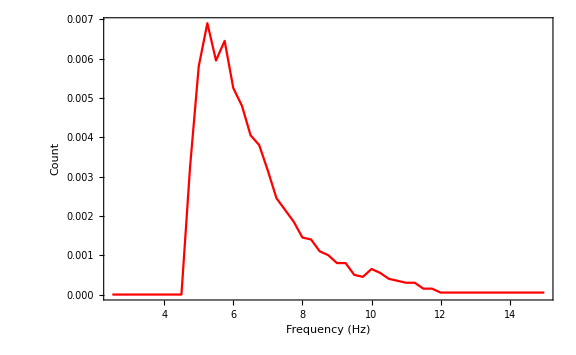

```mathematica
highField12Graph
```

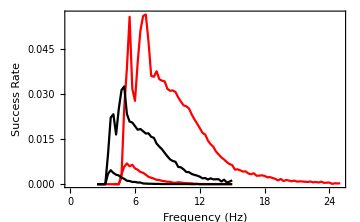

```mathematica
Show[{lowField12Graph,lowField6Graph,highField12Graph,highField6Graph}]
```

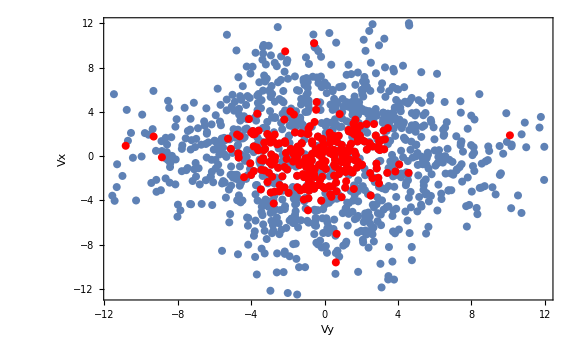

```mathematica
graph1=ListPlot[velData⟦13⟧,PlotStyle->PointSize[.01],ImageSize->Large,Frame->True,AxesLabel->{"Vy","Vx"}];
graph2=ListPlot[velData⟦37⟧,PlotStyle->{RGBColor["Red"],PointSize[.01]},ImageSize->Large];
Show[graph1,graph2]
```

Here, I look at the data of the simulation of 1.2 cm^-1 at 9 kHz to compare with MPI's report of a 20mK trap depth.
My fitting function reports that the gas is 24 mK in the x direction and about 21 mK in the y. A bit hotter than MPI but they do say that they their trapping potential was "on the order of 20mK" without providing actual numerical values so their actual trapping potential may be somewhat higher or lower.

```mathematica
findMaxwellianFit[vData_,binWidth_]:=Module[{histDataForVelocities,bestFitForVelocities,bestFitPlot,histX,histCount},{histX,histCount}=HistogramList[vData,{-20,20,binWidth}];histDataForVelocities=Transpose[{Drop[histX,1],histCount}];bestFitForVelocities=NonlinearModelFit[histDataForVelocities,{α maxboltz1D[v-β,T],0<T<0.3},{α,β,T},v];bestFitPlot=Plot[bestFitForVelocities["BestFit"],{v,-20,20},PlotRange->All];Return[{bestFitForVelocities["BestFitParameters"],Show[{bestFitPlot,ListPlot[histDataForVelocities]}]}]]
```

```mathematica
velsAt9kHz = velData⟦21⟧;
posAt9kHz=getPositions[data]⟦21⟧;
```

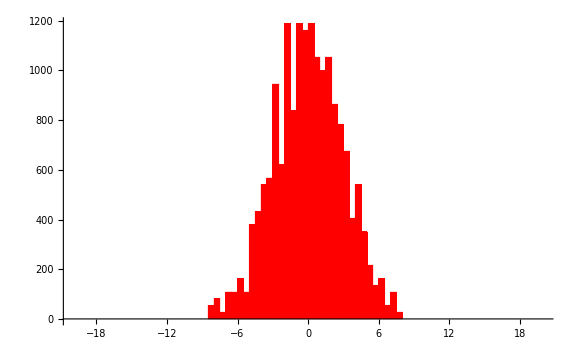

```mathematica
Histogram[Catenate[ConstantArray[Transpose[velsAt9kHz]⟦2⟧,27]],{-20,20,.5},PlotRange->All,ChartStyle->RGBColor[1,0,0],ImageSize->Large](*velocity histogram of x component*)
```

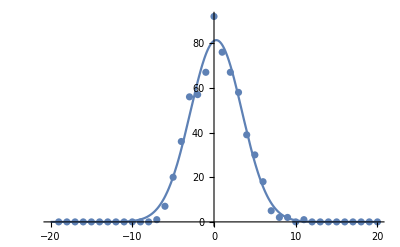
{{α→644.335,β→0.275292,T→0.0240054},-Graphics-}

```mathematica
findMaxwellianFit[velsAt9kHz⟦All,1⟧,1](*x velocity*)
```

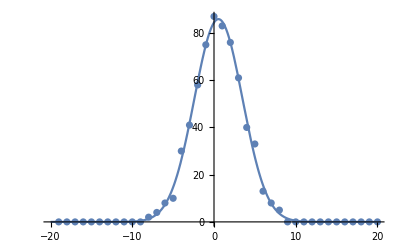
{{α→634.965,β→0.544547,T→0.0209434},-Graphics-}

```mathematica
findMaxwellianFit[velsAt9kHz⟦All,2⟧,1](*y velocity*)
```

Looking at high field velocities alongside low field velocities

```mathematica
highFieldPeakVels=getVelocities[highField12cm]⟦12⟧;
```

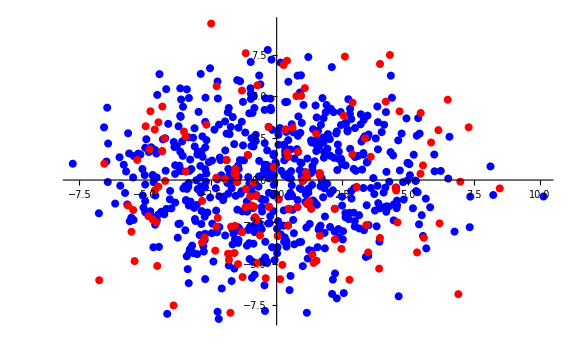

```mathematica
ListPlot[{velsAt9kHz,highFieldPeakVels},ImageSize->Large,PlotStyle->{{Blue,PointSize[.01]},{Red,PointSize[.01]}}]
```

```mathematica
highFieldPeakPos=getPositions[highField12cm]⟦12⟧;
```

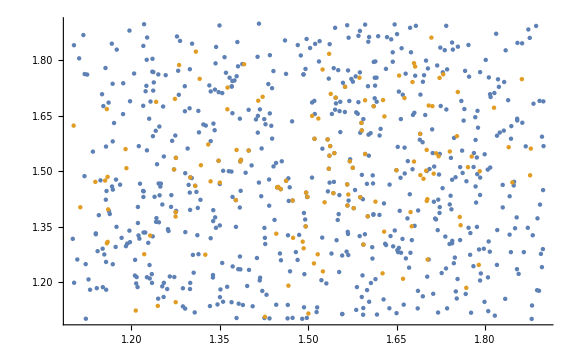

```mathematica
ListPlot[{posAt9kHz,highFieldPeakPos},ImageSize->Large]
```